# Large-Scale Fish Classification

In this project, I will explore various methods for classifying a large-scale fish dataset. The dataset^1 contains images of 9 different types of seafood, collected from a supermarket in Izmir, Turkey. The dataset was collected for a university-industry collaboration project at Izmir University of Economics^2. Each image in the dataset was resized to the have the same size and aspect ratio and the dataset was augmented by flipping and rotating the images. This increases the overall sample size and will help with our training methods. There are a 1000 images for each class, making a total of 9000 images in the dataset. The types of fish are gilt head bream, red sea bream, sea bass, red mullet, horse mackerel, black sea sprat, striped red mullet, trout, and shrimp. I will mainly be focusing on the difference between the 2D, 3D reductions and using the data in grayscale or RGB form.

### Importing data

The first thing to do is to import the dataset and label it accordingly.

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[], "Fish_Dataset"}]];
```

```mathematica
blackSeaSprat = Import/@FileNames["Black Sea Sprat/*.png"];
giltHeadBream = Import/@FileNames["Gilt-Head Bream/*.png"];
hourseMackerel= Import/@FileNames["Hourse Mackerel/*.png"];
redMullet = Import/@FileNames["Red Mullet/*.png"];
redSeaBream= Import/@FileNames["Red Sea Bream/*.png"];
seaBass = Import/@FileNames["Sea Bass/*.png"];
shrimp = Import/@FileNames["Shrimp/*.png"];
stripedRedMullet = Import/@FileNames["Striped Red Mullet/*.png"];
trout = Import/@FileNames["Trout/*.png"];
```

```mathematica
fishImport = {blackSeaSprat, giltHeadBream, hourseMackerel,redMullet,redSeaBream,seaBass,shrimp,stripedRedMullet,trout};
labels = {"Black Sea Sprat","Gilt-Headed Bream","Hourse Mackerel","Red Mullet","Red Sea Bream","Sea Bass","Shrimp","Striped Red Mullet","Trout"};
```

```mathematica
labelledFish = Thread[fishImport-> labels];
flatLabelledFish = Flatten[Thread /@labelledFish];
```

Here is a small sample of the data to show what the pictures of this dataset look like :

```mathematica
RandomSample[flatLabelledFish,8]
```

{-Graphics-→Trout,-Graphics-→Hourse Mackerel,-Graphics-→Red Mullet,-Graphics-→Hourse Mackerel,-Graphics-→Black Sea Sprat,-Graphics-→Red Mullet,-Graphics-→Red Mullet,-Graphics-→Gilt-Headed Bream}

## Analysis

## Using classify

First lets see how the classify function performs with the raw, labelled image data

### Test and training datasets

Creating a sample with the same amount of fish from each class. We will use this sample to create test and training datasets using an 80-20 ratio.

```mathematica
samplesBig = RandomSample[#,200]& /@ fishImport;
trainingDataBig = Thread[samplesBig->labels];
flatTrainingDataBig = Flatten[Thread /@trainingDataBig];
```

The following indicates that there are 20 non-distinct elements in flatLabelledFish, which will be worth keeping in mind.

```mathematica
Dimensions[flatLabelledFish]
Dimensions[Complement[flatLabelledFish, {}]]
```

{9000}

{8980}

Now create a set of test data, separate from the training data

```mathematica
testDataBig = Complement[flatLabelledFish, flatTrainingDataBig];
Dimensions[testDataBig]
```

{7180}

### Logistic Regression

We will use perform logistic regression on the training data. The idea of this is to try and fit the sigmoid function to the data instead of a straight line.

```mathematica
logReg = Classify[flatTrainingDataBig, Method -> "LogisticRegression"];
```

```mathematica
Information[logReg, "LearningCurve"]
```

```mathematica
cmlogReg = ClassifierMeasurements[logReg, testDataBig];
```

```mathematica
cmlogReg["Accuracy"]
```

0.989694

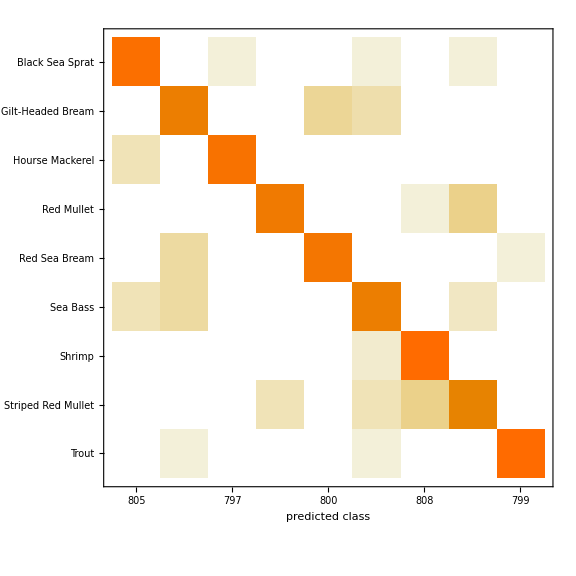

```mathematica
Show[cmlogReg["ConfusionMatrixPlot"], ImageSize -> Large]
```

The logistic regression performs excellently on the dataset with 98.9% accuracy. The confusion matrix highlights this and in particular it is clear that shrimp and trout are identified extremely well against the other types of fish.

We can manually check how the model performs with the test data with the following:

```mathematica
Tally[Map[logReg[#[[1]]]==#[[2]]&,testDataBig]]
```

{{True,7106},{False,74}}

### Support Vector Machine

```mathematica
svm= Classify[flatTrainingDataBig, Method -> "SupportVectorMachine"];
```

```mathematica
Information[svm, "LearningCurve"]
```

The loss is minimal for the algorithm which uses the radial basis kernel with a soft parameter of 3 and gamma scaling parameter of 0.001007

```mathematica
cmsvm = ClassifierMeasurements[svm, testDataBig];
```

```mathematica
cmsvm["Accuracy"]
```

```mathematica
Show[cmsvm["ConfusionMatrixPlot"], ImageSize -> Large]
```

```mathematica
Tally[Map[svm[#[[1]]]==#[[2]]&,testDataBig]]
```

The support vector machine also performs excellently on the dataset with accuracy. This is slightly better than the logistic regression model above.

## Dimension reduction

Now I will perform dimension reduction to reduce the image data to 2 and 3 dimensions. I will explore the full RGB version and the grayscale version of the data.
This dimension reduction technique uses the function DimensionReduction to find the most important directions/positions in the images as vectors in order to project from the higher-dimensional space into a lower-dimensional approximating manifold. This will be useful for further analysis to perform classification via support vector machines.

### Creating sample and test data

To perform manual classification, I will only use a smaller sample size for training compared to when using the classify functions before.

```mathematica
samples = RandomSample[#,20]& /@ fishImport;
trainingData = Thread[samples->labels];
FlatTrainingData = Flatten[Thread /@trainingData];
```

The following line indicates that there are 20 non-distinct elements in flatLabelledFish, which will be worth keeping in mind.

```mathematica
Dimensions[flatLabelledFish]
Dimensions[Complement[flatLabelledFish, {}]]
```

{9000}

{8980}

Separating the test data from the training data:

```mathematica
testData = Complement[flatLabelledFish, FlatTrainingData];
Dimensions[testData]
```

{8800}

We will choose 2 classes to perform one-vs-one classification.

```mathematica
fishChoice = {"Trout","Shrimp"};
```

Sorting by key isn’t necessary in the following, but we will do so for consistency and generality in cases where the samples aren' t organised.

```mathematica
trainingByName  = GroupBy[FlatTrainingData, Last -> First];
trainingChoice =  KeyTake[trainingByName, fishChoice];
trainingChoiceBW = ColorConvert[#, "Grayscale"] &/@ trainingChoice;
```

```mathematica
testDataByName =GroupBy[testData, Last -> First];
testChoice = KeyTake[testDataByName, fishChoice];
testChoiceBW = ColorConvert[#, "Grayscale"] &/@ testChoice;
```

### Dimension Reduction for images in colour

#### Creating image test and training data

```mathematica
trainingChoiceImg = Flatten[Values[trainingChoice]];
trainingChoiceImgData = Flatten /@ ImageData /@ trainingChoiceImg;
```

trainingChoiceImgData is a matrix with 40 rows and 787,650 columns. Each row is one image, where each image has 787,650 entry values of data.

```mathematica
Dimensions[trainingChoiceImgData]
```

{40,787650}

Note on error in computing Singular Values

Due to the size of the data, Mathematica’s Kernel instantly crashes when trying to calculate the number of principal components with the following:

standardizedData = Standardize[trainingChoiceImgData, Mean, 1 &];
Dimensions[Diagonal[SingularValueDecomposition[standardizedData][[2]]]]

#### 2D reduction for RGB

```mathematica
d2FishChoice = DimensionReduction[trainingChoiceImgData, 2, Method -> "PrincipalComponentsAnalysis"];
proj2FishChoice = Map[d2FishChoice[Flatten[ImageData[#]]]&,trainingChoice,{2}];
```

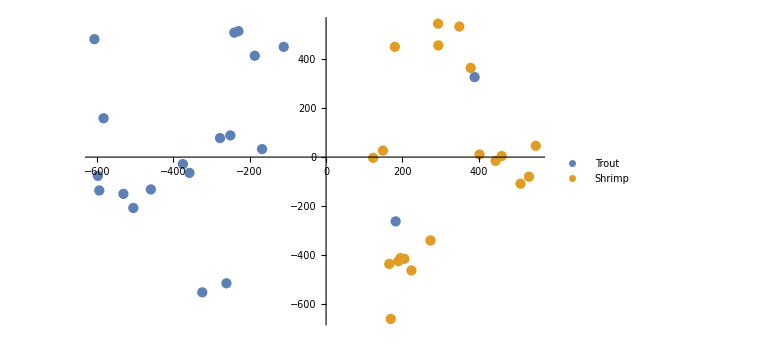

```mathematica
ListPlot[Values[proj2FishChoice],PlotLegends->Keys[proj2FishChoice], ImageSize -> Large]
```

We can see here that the data is not linearly separable, but almost is. We will need to add slack when solving the dual problem later on.

#### 3D reduction for RGB

```mathematica
d3FishChoice = DimensionReduction[trainingChoiceImgData, 3, Method -> "PrincipalComponentsAnalysis"];
proj3FishChoice = Map[d3FishChoice[Flatten[ImageData[#]]]&,trainingChoice,{2}];.10
```

.10

```mathematica
ListPointPlot3D[Values[proj3FishChoice], PlotLegends->Keys[proj3FishChoice], ImageSize -> Large]
```

-Graphics3D-

### Dimension reduction for images in grayscale

#### Converting data to grayscale

```mathematica
samplesBW = ColorConvert[#, "Grayscale"] & /@ samples;
trainingDataBW = Thread[samplesBW -> labels];
flatTrainingDataBW = Flatten[Thread /@ trainingDataBW];
```

```mathematica
trainingByNameBW = GroupBy[flatTrainingDataBW, Last -> First];
trainingChoiceBW =  KeyTake[trainingByNameBW, fishChoice];
```

```mathematica
trainingChoiceImgBW = Flatten[Values[trainingChoiceBW]];
trainingChoiceImgDataBW =Flatten /@ImageData /@ trainingChoiceImgBW;
```

trainingChoiceImgData is a matrix with 40 rows and 787, 650 columns . Each row is one image, where each image has 787, 650 entry values of data .

```mathematica
Dimensions[trainingChoiceImgDataBW]
```

{40,262550}

#### 2D reduction for grayscale

```mathematica
d2FishChoiceBW = DimensionReduction[trainingChoiceImgDataBW, 2, Method -> "PrincipalComponentsAnalysis"];
```

```mathematica
proj2FishChoiceBW = Map[d2FishChoiceBW[Flatten[ImageData[#]]]&,trainingChoiceBW,{2}];
```

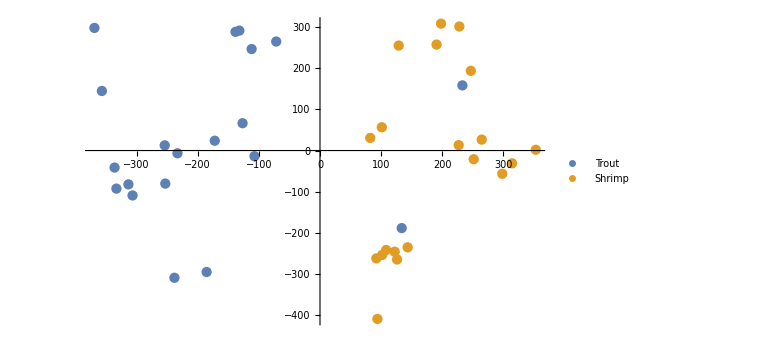

```mathematica
ListPlot[Values[proj2FishChoiceBW], PlotLegends->Keys[proj2FishChoiceBW], ImageSize->Large]
```

#### 3D reduction for grayscale

```mathematica
d3FishChoiceBW = DimensionReduction[trainingChoiceImgDataBW, 3, Method -> "PrincipalComponentsAnalysis"];
proj3FishChoiceBW = Map[d3FishChoiceBW[Flatten[ImageData[#]]]&,trainingChoiceBW,{2}];
```

```mathematica
ListPointPlot3D[Values[proj3FishChoiceBW], PlotLegends->Keys[proj3FishChoiceBW], ImageSize -> Large]
```

-Graphics3D-

## Classification via Support Vector Machine

Now we will explore solving the dual problem manually for each of the reductions above. We will need to add slack to this problem because the data is not linearly separable. We do this by adding an upper bound C on each λ. The value of this bound C represents how much slack we are allowing, it is a regularization parameter. In the limit as C  → ∞, we end up with the hard margin dual problem and as C → 0 , we are allowing more slack for the data points to be on the wrong side of the decision line. We need to be careful in our choice of C.  If C is chosen to be too small then the model will choose fewer data points as support vectors which may lead to under-fitting. On the other hand, if C is chosen it be too big then the model will choose more data points as support vectors which may lead to over-fitting the training data.

### Solving the dual problem for 2D RGB

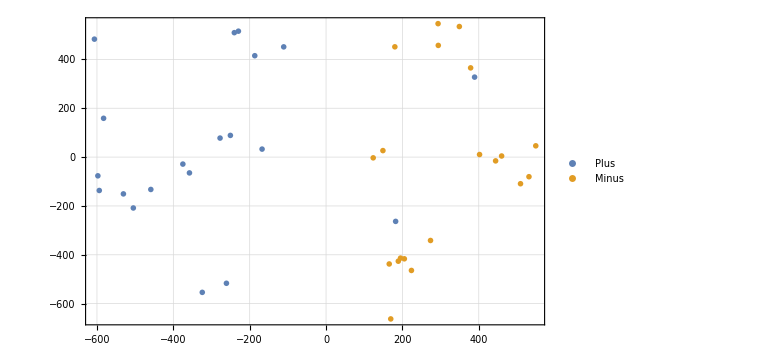

```mathematica
data2D = KeyMap[Replace[{fishChoice[[1]] -> "Plus", fishChoice[[2]] -> "Minus"}],proj2FishChoice];
ListPlot[data2D, PlotMarkers -> "OpenMarkers", PlotTheme -> "Detailed", ImageSize -> Large]
```

```mathematica
X2D=Join[data2D["Plus"],-data2D["Minus"]];
Y2D=Join[ConstantArray[1,Length[data2D["Plus"]]],ConstantArray[-1,Length[data2D["Minus"]]]];
e2D=ConstantArray[1,Length[X2D]];
λ2D=Table[λi[i],{i,Length[X2D]}];
c = 1;
```

For now, we will just choose c to be equal to 1. We will explore this in more detail later on.

```mathematica
{max2D,solλ2D}=NMaximize[{-1/2 λ2D.X2D.Transpose[X2D].λ2D+λ2D.e2D,c>=λ2D>0,λ2D.Y2D==0},λ2D];
```

Now for choosing the support vectors, we choose the λ values that are non-zero and not C within a significance level. The reason for this is because λ values that take the value of the upper bound are the problematic values that caused us to introduce this bound in the first place. We don’t consider these to be support vectors.

```mathematica
svmλ2DVal = If[10^-1<#<c-10^-1,#,0]& /@ λ2D/.solλ2D
```

{0,0,0,0,0.530341,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.654823,0,0,0.779812,0,0,0,0,0,0,0,0,0}

We now select the points corresponding to these values as the support vectors

```mathematica
supportVectors2D=Pick[Join[data2D["Plus"],data2D["Minus"]],If[10^-1<#<c-10^-1,True,False]& /@ λ2D/.solλ2D];
```

Extract the position in solλ of the support vector with the highest weight λ

```mathematica
posMax2D = Position[solλ2D,Max[svmλ2DVal]][[1,1]]
```

31

Now we check if this position corresponds to a plus or minus value in the data and correspondingly associate the sign

```mathematica
maxValSign2D = Which[posMax2D<= Length[data2D[[1]]] , 1, True,-1]
```

-1

Now we can solve for w and b, and create a decision function as follows

```mathematica
wsolλ2D=Thread[{w1,w2}->Transpose[X2D].λ2D/.solλ2D];
bsolλ2D=Solve[Values[wsolλ2D].X2D[[posMax2D]]*maxValSign2D+b==maxValSign2D,b][[1]];
```

```mathematica
decision2D[x_]:=Values[wsolλ2D].x+ Values[bsolλ2D]
```

```mathematica
decisionLine2D = Solve[decision2D[{x,y}]==0,y];
plusMargin2D = Solve[decision2D[{x,y}]==1,y];
minusMargin2D = Solve[decision2D[{x,y}]==-1,y];
```

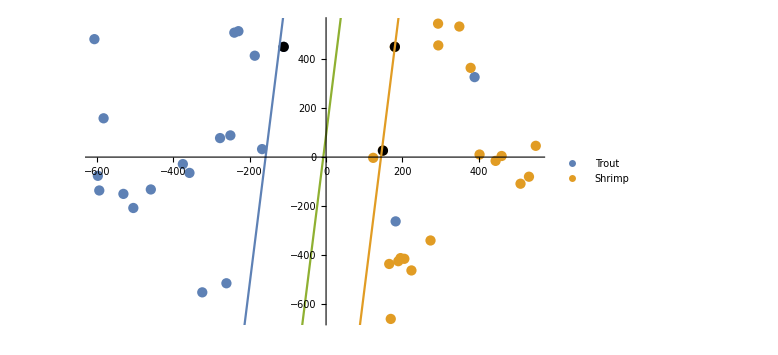

```mathematica
Show[ListPlot[Values[proj2FishChoice],  PlotLegends ->Keys[proj2FishChoice]],ListPlot[supportVectors2D, PlotStyle -> Black],Plot[{Values[plusMargin2D],Values[minusMargin2D], Values[decisionLine2D]},{x,Min[Values[data2D]], Max[Values[data2D]]}], ImageSize->Large]
```

#### Projecting test points

Now project the test data onto the graph

```mathematica
proj2TestChoice = Map[d2FishChoice[Flatten[ImageData[#]]]&,testChoice,{2}];
```

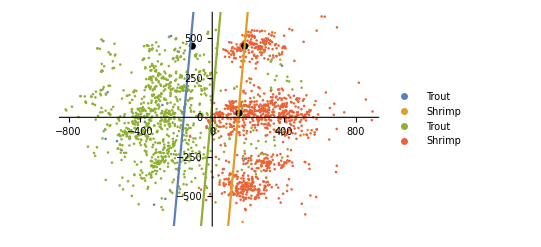

```mathematica
Show[ListPlot[Join[Values[proj2FishChoice],Values[proj2TestChoice]], PlotLegends ->Join[Keys[proj2FishChoice], Keys[proj2TestChoice]]],ListPlot[supportVectors2D, PlotStyle -> Black],Plot[{Values[plusMargin2D],Values[minusMargin2D], Values[decisionLine2D]},{x,Min[Values[data2D]], Max[Values[data2D]]}]]
```

#### Classifier function

Creating a function to classify which fish a point corresponds to

```mathematica
whichFish2D[x_]:=Which[decision2D[x][[1]] >0, fishChoice[[1]], True,fishChoice[[2]]]
```

```mathematica
whichFish2D[{500,0}]
```

Shrimp

Classifying the test data and doing a tally of the correct and incorrect classifications

```mathematica
Tally[Flatten[whichFish2D /@ proj2TestChoice[[#]]& /@{1,2}]]
```

{{Trout,874},{Shrimp,1086}}

```mathematica
Tally[Join[Map[whichFish2D[#] == Keys[proj2TestChoice][[1]]&,proj2TestChoice[[1]]], Map[whichFish2D[#] == Keys[proj2TestChoice][[2]]&,proj2TestChoice[[2]]]]]
```

{{True,1848},{False,112}}

### Solving the dual problem for 3D RGB

```mathematica
data3D = KeyMap[Replace[{fishChoice[[1]] -> "Plus", fishChoice[[2]] -> "Minus"}],proj3FishChoice];
ListPointPlot3D[data3D, PlotTheme -> "Detailed",PlotLegends->Keys[data3D], ImageSize -> Large]
```

-Graphics3D-

```mathematica
X3D=Join[data3D["Plus"],-data3D["Minus"]];
Y3D=Join[ConstantArray[1,Length[data3D["Plus"]]],ConstantArray[-1,Length[data3D["Minus"]]]];
e3D=ConstantArray[1,Length[X3D]];
λ3D=Table[λi[i],{i,Length[X3D]}];
```

```mathematica
{max3D,solλ3D}=NMaximize[{-1/2 λ3D.X3D.Transpose[X3D].λ3D+λ3D.e3D,c>=λ3D>0,λ3D.Y3D==0},λ3D];
```

```mathematica
svmλ3DVal = If[10^-1<#<c-10^-1,#,0]& /@ λ3D/.solλ3D
```

{0,0,0,0,0,0,0,0,0.252118,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.227258,0,0.109846,0,0,0,0,0.724653,0,0.178756,0,0,0,0.5161,0.411741,0.124602,0}

```mathematica
supportVectors3D=Pick[Join[data3D["Plus"],data3D["Minus"]],If[10^-1<#<c-10^-1,True,False]& /@ λ3D/.solλ3D];
```

```mathematica
Max[svmλ3DVal]
```

0.724653

```mathematica
posMax3D = Position[solλ3D,Max[svmλ3DVal]][[1,1]]
```

31

```mathematica
maxValSign3D = Which[posMax3D<= Length[data3D[[1]]] , 1, True,-1]
```

-1

```mathematica
wsolλ3D=Thread[{w1,w2,w3}->Transpose[X3D].λ3D/.solλ3D];
bsolλ3D=Solve[Values[wsolλ3D].X3D[[posMax3D]]*maxValSign3D+b==maxValSign3D/.wsolλ3D,b][[1]];
decisionz=z0/.Solve[{w1,w2,w3}.{x0,y0,z0}+b==fx/.Join[wsolλ3D,bsolλ3D],z0][[1]];
```

```mathematica
Show[ListPointPlot3D[Values[proj3FishChoice], PlotLegends -> Keys[proj3FishChoice]],ListPointPlot3D[supportVectors3D,PlotStyle->Black],Plot3D[Evaluate[decisionz/.fx->{1,-1,0}],{x0,-500,500},{y0,-600,500}],ImageSize -> Large]
```

-Graphics3D-

#### Projecting test data

```mathematica
proj3TestChoice = Map[d3FishChoice[Flatten[ImageData[#]]]&,testChoice,{2}];
```

```mathematica
Show[ListPointPlot3D[Join[Values[proj3FishChoice],Values[proj3TestChoice]], PlotLegends ->Join[Keys[proj3FishChoice], Keys[proj3TestChoice]]],ListPointPlot3D[supportVectors3D, PlotStyle -> Black],Plot3D[Evaluate[decisionz/.fx->{1,-1,0}],{x0,-500,500},{y0,-500,500}], ImageSize -> Large]
```

-Graphics3D-

#### Decision function

```mathematica
decision3D[x_]:=Values[wsolλ3D].x+ Values[bsolλ3D]
```

```mathematica
whichFish3D[x_]:=Which[decision3D[x][[1]] >0, fishChoice[[1]], True,fishChoice[[2]]]
```

```mathematica
Tally[Flatten[whichFish3D /@ proj3TestChoice[[#]]& /@{1,2}]]
```

{{Shrimp,1167},{Trout,793}}

```mathematica
Tally[Join[Map[whichFish3D[#] == Keys[proj3TestChoice][[1]]&,proj3TestChoice[[1]]], Map[whichFish3D[#] == Keys[proj3TestChoice][[2]]&,proj3TestChoice[[2]]]]]
```

{{False,187},{True,1773}}

### Solving the dual problem for 2D grayscale

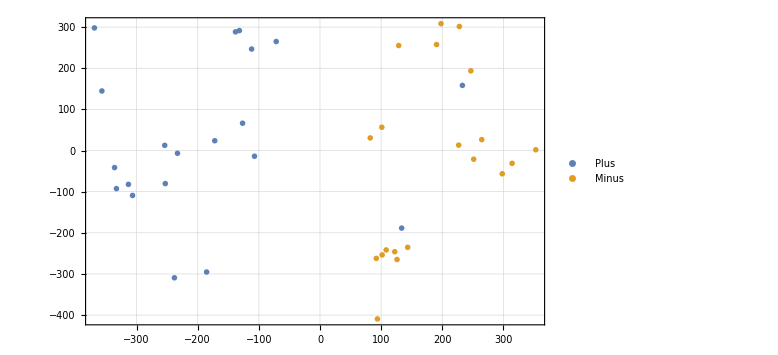

```mathematica
data2DBW = KeyMap[Replace[{fishChoice[[1]] -> "Plus", fishChoice[[2]] -> "Minus"}],proj2FishChoiceBW];
ListPlot[data2DBW, PlotMarkers -> "OpenMarkers", PlotTheme -> "Detailed", ImageSize -> Large]
```

```mathematica
X2DBW=Join[data2DBW["Plus"],-data2DBW["Minus"]];
Y2DBW=Join[ConstantArray[1,Length[data2DBW["Plus"]]],ConstantArray[-1,Length[data2DBW["Minus"]]]];
e2DBW=ConstantArray[1,Length[X2DBW]];
λ2DBW=Table[λi[i],{i,Length[X2DBW]}];
```

```mathematica
{max2DBW,solλ2DBW}=NMaximize[{-1/2 λ2DBW.X2DBW.Transpose[X2DBW].λ2DBW+λ2DBW.e2DBW,c>=λ2DBW>0,λ2DBW.Y2DBW==0},λ2DBW];
```

```mathematica
svmλ2DValBW = If[10^-1<#<c-10^-1,#,0]& /@λ2DBW/.solλ2DBW
```

{0,0,0,0,0.417067,0,0,0,0.126089,0,0,0,0,0,0,0.323237,0,0,0,0,0,0,0,0,0,0,0,0.697817,0,0,0.646141,0,0,0,0,0,0,0,0.340553,0}

```mathematica
supportVectors2DBW=Pick[Join[data2DBW["Plus"],data2DBW["Minus"]],If[10^-1<#<c-10^-1,True,False]& /@ λ2DBW/.solλ2DBW];
```

```mathematica
posMax2DBW = Position[solλ2DBW,Max[svmλ2DValBW]][[1,1]]
```

28

```mathematica
maxValSign2DBW = Which[posMax2DBW<= Length[data2DBW[[1]]] , 1, True,-1]
```

-1

```mathematica
wsolλ2DBW=Thread[{w1,w2}->Transpose[X2DBW].λ2DBW/.solλ2DBW];
bsolλ2DBW=Solve[Values[wsolλ2DBW].X2DBW[[posMax2DBW]]*maxValSign2DBW+b==maxValSign2DBW,b][[1]];
```

```mathematica
decision2DBW[x_]:=Values[wsolλ2DBW].x+ Values[bsolλ2DBW]
```

```mathematica
decisionLine2DBW = Solve[decision2DBW[{x,y}]==0,y];
plusMargin2DBW = Solve[decision2DBW[{x,y}]==1,y];
minusMargin2DBW = Solve[decision2DBW[{x,y}]==-1,y];
```

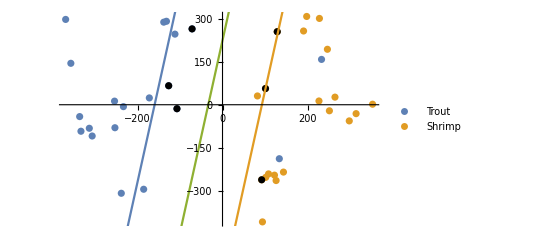

```mathematica
Show[ListPlot[Values[proj2FishChoiceBW],  PlotLegends ->Keys[proj2FishChoiceBW]],ListPlot[supportVectors2DBW, PlotStyle -> Black],Plot[{Values[plusMargin2DBW],Values[minusMargin2DBW], Values[decisionLine2DBW]},{x,Min[Values[data2DBW]], Max[Values[data2DBW]]}]]
```

#### Projecting test data

Now project the test data onto the graph

```mathematica
proj2TestChoiceBW = Map[d2FishChoiceBW[Flatten[ImageData[#]]]&,testChoiceBW,{2}];
```

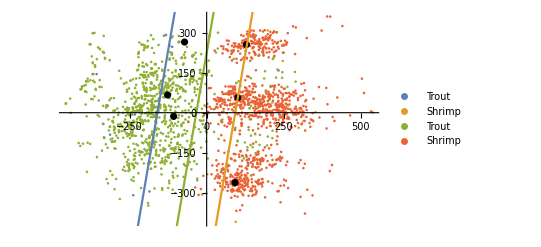

```mathematica
Show[ListPlot[Join[Values[proj2FishChoiceBW],Values[proj2TestChoiceBW]], PlotLegends ->Join[Keys[proj2FishChoiceBW], Keys[proj2TestChoiceBW]]],ListPlot[supportVectors2DBW, PlotStyle -> Black],Plot[{Values[plusMargin2DBW],Values[minusMargin2DBW], Values[decisionLine2DBW]},{x,Min[Values[data2DBW]], Max[Values[data2DBW]]}]]
```

#### Decision function

```mathematica
whichFish2DBW[x_]:=Which[decision2DBW[x][[1]] >0, fishChoice[[1]], True,fishChoice[[2]]]
```

```mathematica
whichFish2DBW[{-500,0}]
```

Trout

```mathematica
Tally[Flatten[whichFish2DBW /@ proj2TestChoiceBW[[#]]& /@{1,2}]]
```

{{Shrimp,1098},{Trout,862}}

```mathematica
Tally[Join[Map[whichFish2DBW[#] == Keys[proj2TestChoiceBW][[1]]&,proj2TestChoiceBW[[1]]], Map[whichFish2DBW[#] == Keys[proj2TestChoiceBW][[2]]&,proj2TestChoiceBW[[2]]]]]
```

{{False,122},{True,1838}}

### Solving the dual problem for 3D grayscale

```mathematica
data3DBW = KeyMap[Replace[{fishChoice[[1]] -> "Plus", fishChoice[[2]] -> "Minus"}],proj3FishChoiceBW];
ListPointPlot3D[data3DBW, PlotTheme -> "Detailed",PlotLegends->Keys[data3DBW ],ImageSize -> Large]
```

-Graphics3D-

```mathematica
X3DBW=Join[data3DBW["Plus"],-data3DBW["Minus"]];
Y3DBW=Join[ConstantArray[1,Length[data3DBW["Plus"]]],ConstantArray[-1,Length[data3DBW["Minus"]]]];
e3DBW=ConstantArray[1,Length[X3DBW]];
λ3DBW=Table[λi[i],{i,Length[X3DBW]}];
```

we’ve added slack here below

```mathematica
{max3DBW,solλ3DBW}=NMaximize[{-1/2 λ3DBW.X3DBW.Transpose[X3DBW].λ3DBW+λ3DBW.e3DBW,c>=λ3DBW>0,λ3DBW.Y3DBW==0},λ3DBW];
```

```mathematica
svmλ3DValBW = If[10^-3<#<c-10^-3,#,0]& /@ λ3DBW/.solλ3DBW
```

{0,0,0,0,0.0315811,0.00225633,0.0883147,0,0.35554,0,0,0,0,0,0,0.0156193,0,0,0,0,0.17097,0,0,0.0291756,0,0.317521,0,0.0953828,0.169841,0,0.79646,0,0,0,0,0,0.308501,0.357596,0.247603,0}

```mathematica
supportVectors3DBW=Pick[Join[data3DBW["Plus"],data3DBW["Minus"]],If[10^-3<#<c-10^-3,True,False]& /@ λ3DBW/.solλ3DBW];
```

```mathematica
Max[svmλ3DValBW]
```

0.79646

```mathematica
posMax3DBW = Position[solλ3DBW,Max[svmλ3DValBW]][[1,1]]
```

31

```mathematica
maxValSign3DBW = Which[posMax3DBW<= Length[data3DBW[[1]]] , 1, True,-1]
```

-1

```mathematica
wsolλ3DBW=Thread[{w1,w2,w3}->Transpose[X3DBW].λ3DBW/.solλ3DBW];
bsolλ3DBW=Solve[Values[wsolλ3DBW].X3DBW[[posMax3DBW]]*maxValSign3DBW+b==maxValSign3DBW,b][[1]];
decisionzBW=z0/.Solve[{w1,w2,w3}.{x0,y0,z0}+b==fx/.Join[wsolλ3DBW,bsolλ3DBW],z0][[1]];
```

```mathematica
Show[ListPointPlot3D[Values[proj3FishChoiceBW],PlotLegends -> Keys[proj3FishChoiceBW]],ListPointPlot3D[supportVectors3DBW,PlotStyle->Black],Plot3D[Evaluate[decisionzBW/.fx->{1,-1,0}],{x0,-500,500},{y0,-500,500}],ImageSize -> Large]
```

-Graphics3D-

```mathematica
proj3TestChoiceBW = Map[d3FishChoiceBW[Flatten[ImageData[#]]]&,testChoiceBW,{2}];
```

```mathematica
Show[ListPointPlot3D[Join[Values[proj3FishChoiceBW],Values[proj3TestChoiceBW]], PlotLegends ->Join[Keys[proj2FishChoiceBW], Keys[proj3TestChoiceBW]]],ListPointPlot3D[supportVectors3DBW, PlotStyle -> Black],Plot3D[Evaluate[decisionzBW/.fx->{1,-1,0}],{x0,-500,500},{y0,-500,500}], ImageSize -> Large]
```

-Graphics3D-

```mathematica
decision3DBW[x_]:=Values[wsolλ3DBW].x+ Values[bsolλ3DBW]
```

```mathematica
whichFish3DBW[x_]:=Which[decision3DBW[x][[1]] >0, fishChoice[[1]], True,fishChoice[[2]]]
```

```mathematica
Tally[Flatten[whichFish3DBW /@ proj3TestChoiceBW[[#]]& /@{1,2}]]
```

{{Shrimp,1163},{Trout,797}}

```mathematica
Tally[Join[Map[whichFish3DBW[#] == Keys[proj3TestChoiceBW][[1]]&,proj3TestChoiceBW[[1]]], Map[whichFish3DBW[#] == Keys[proj3TestChoiceBW][[2]]&,proj3TestChoiceBW[[2]]]]]
```

{{False,183},{True,1777}}

## Exploring the regularization parameter

Since the performance has been better with grayscale, we will ust that data to explore the parameter

```mathematica
ListPlot[data2DBW, PlotMarkers -> "OpenMarkers", PlotTheme -> "Detailed", ImageSize -> Large]
```

-Graphics-

### c = 0.5

```mathematica
c1 = 0.5;
```

#### Solving the dual problem

```mathematica
{max2DBW1,solλ2DBW1}=NMaximize[{-1/2 λ2DBW.X2DBW.Transpose[X2DBW].λ2DBW+λ2DBW.e2DBW,c1>=λ2DBW>0,λ2DBW.Y2DBW==0},λ2DBW];
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
svmλ2DValBW1= If[10^-1<#<c1-10^-1,#,0]& /@λ2DBW/.solλ2DBW1
```

{0,0,0,0,0.303494,0,0,0,0,0,0,0,0,0,0,0.154971,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.316098,0,0,0,0,0,0,0,0.198457,0}

```mathematica
supportVectors2DBW1=Pick[Join[data2DBW["Plus"],data2DBW["Minus"]],If[10^-1<#<c1-10^-1,True,False]& /@ λ2DBW/.solλ2DBW1];
```

```mathematica
posMax2DBW1 = Position[solλ2DBW,Max[svmλ2DValBW]][[1,1]]
```

28

```mathematica
maxValSign2DBW1 = Which[posMax2DBW1<= Length[data2DBW[[1]]] , 1, True,-1]
```

-1

```mathematica
wsolλ2DBW1=Thread[{w1,w2}->Transpose[X2DBW].λ2DBW/.solλ2DBW1];
bsolλ2DBW1=Solve[Values[wsolλ2DBW1].X2DBW[[posMax2DBW1]]*maxValSign2DBW1+b==maxValSign2DBW1,b][[1]];
```

```mathematica
decision2DBW1[x_]:=Values[wsolλ2DBW1].x+ Values[bsolλ2DBW1]
```

```mathematica
decisionLine2DBW1 = Solve[decision2DBW1[{x,y}]==0,y];
plusMargin2DBW1 = Solve[decision2DBW1[{x,y}]==1,y];
minusMargin2DBW1= Solve[decision2DBW1[{x,y}]==-1,y];
```

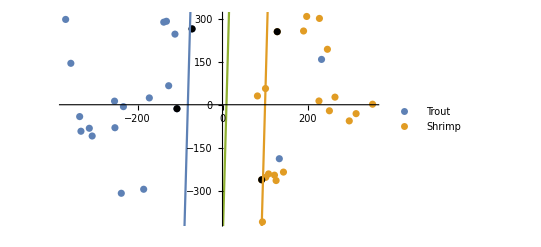

```mathematica
Show[ListPlot[Values[proj2FishChoiceBW],  PlotLegends ->Keys[proj2FishChoiceBW]],ListPlot[supportVectors2DBW1, PlotStyle -> Black],Plot[{Values[plusMargin2DBW1],Values[minusMargin2DBW1], Values[decisionLine2DBW1]},{x,Min[Values[data2DBW]], Max[Values[data2DBW]]}]]
```

#### Projecting test data

Now project the test data onto the graph

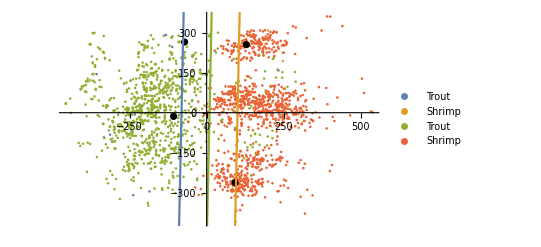

```mathematica
Show[ListPlot[Join[Values[proj2FishChoiceBW],Values[proj2TestChoiceBW]], PlotLegends ->Join[Keys[proj2FishChoiceBW], Keys[proj2TestChoiceBW]]],ListPlot[supportVectors2DBW1, PlotStyle -> Black],Plot[{Values[plusMargin2DBW1],Values[minusMargin2DBW1], Values[decisionLine2DBW1]},{x,Min[Values[data2DBW]], Max[Values[data2DBW]]}]]
```

#### Decision function

```mathematica
whichFish2DBW1[x_]:=Which[decision2DBW1[x][[1]] >0, fishChoice[[1]], True,fishChoice[[2]]]
```

```mathematica
Tally[Flatten[whichFish2DBW1 /@ proj2TestChoiceBW[[#]]& /@{1,2}]]
```

{{Trout,912},{Shrimp,1048}}

```mathematica
Tally[Join[Map[whichFish2DBW1[#] == Keys[proj2TestChoiceBW][[1]]&,proj2TestChoiceBW[[1]]], Map[whichFish2DBW1[#] == Keys[proj2TestChoiceBW][[2]]&,proj2TestChoiceBW[[2]]]]]
```

{{True,1866},{False,94}}

### c = 10

```mathematica
c2 = 10;
```

#### Solving the dual problem

```mathematica
{max2DBW2,solλ2DBW2}=NMaximize[{-1/2 λ2DBW.X2DBW.Transpose[X2DBW].λ2DBW+λ2DBW.e2DBW,c2>=λ2DBW>0,λ2DBW.Y2DBW==0},λ2DBW];
```

```mathematica
svmλ2DValBW2 = If[10^-1<#<c2-10^-1,#,0]& /@λ2DBW/.solλ2DBW2
```

{0,0,0,0,8.21073,0,0,0,0,0,0,0,0,0,0,0.147986,0,0,0,0,9.87364,0,0,0.257924,0.11554,0.370034,0,9.77496,0.24687,0,6.44606,0,0,0,0,0,0,0.134632,1.17781,0}

```mathematica
supportVectors2DBW2=Pick[Join[data2DBW["Plus"],data2DBW["Minus"]],If[10^-1<#<c2-10^-1,True,False]& /@ λ2DBW/.solλ2DBW2];
```

```mathematica
posMax2DBW2 = Position[solλ2DBW2,Max[svmλ2DValBW2]][[1,1]]
```

21

```mathematica
maxValSign2DBW2= Which[posMax2DBW2<= Length[data2DBW[[1]]] , 1, True,-1]
```

-1

```mathematica
wsolλ2DBW2=Thread[{w1,w2}->Transpose[X2DBW].λ2DBW/.solλ2DBW2];
bsolλ2DBW2=Solve[Values[wsolλ2DBW2].X2DBW[[posMax2DBW2]]*maxValSign2DBW2+b==maxValSign2DBW2,b][[1]];
```

```mathematica
decision2DBW2[x_]:=Values[wsolλ2DBW2].x+ Values[bsolλ2DBW2]
```

```mathematica
decisionLine2DBW2 = Solve[decision2DBW2[{x,y}]==0,y];
plusMargin2DBW2= Solve[decision2DBW2[{x,y}]==1,y];
minusMargin2DBW2= Solve[decision2DBW2[{x,y}]==-1,y];
```

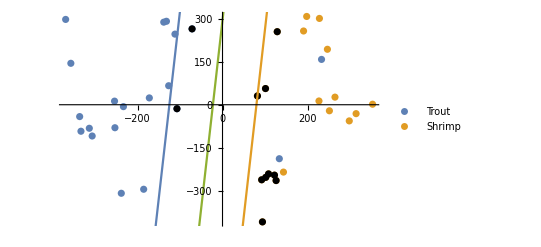

```mathematica
Show[ListPlot[Values[proj2FishChoiceBW],  PlotLegends ->Keys[proj2FishChoiceBW]],ListPlot[supportVectors2DBW2, PlotStyle -> Black],Plot[{Values[plusMargin2DBW2],Values[minusMargin2DBW2], Values[decisionLine2DBW2]},{x,Min[Values[data2DBW]], Max[Values[data2DBW]]}]]
```

#### Projecting test data

Now project the test data onto the graph

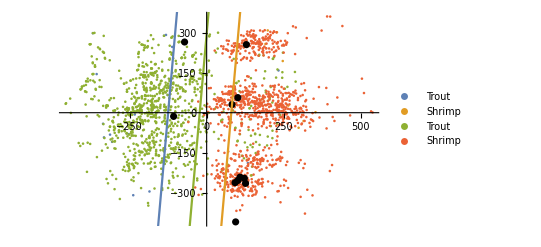

```mathematica
Show[ListPlot[Join[Values[proj2FishChoiceBW],Values[proj2TestChoiceBW]], PlotLegends ->Join[Keys[proj2FishChoiceBW], Keys[proj2TestChoiceBW]]],ListPlot[supportVectors2DBW2, PlotStyle -> Black],Plot[{Values[plusMargin2DBW2],Values[minusMargin2DBW2], Values[decisionLine2DBW2]},{x,Min[Values[data2DBW]], Max[Values[data2DBW]]}]]
```

#### Decision function

```mathematica
whichFish2DBW2[x_]:=Which[decision2DBW2[x][[1]] >0, fishChoice[[1]], True,fishChoice[[2]]]
```

```mathematica
Tally[Flatten[whichFish2DBW2 /@ proj2TestChoiceBW[[#]]& /@{1,2}]]
```

{{Trout,871},{Shrimp,1089}}

```mathematica
Tally[Join[Map[whichFish2DBW2[#] == Keys[proj2TestChoiceBW][[1]]&,proj2TestChoiceBW[[1]]], Map[whichFish2DBW2[#] == Keys[proj2TestChoiceBW][[2]]&,proj2TestChoiceBW[[2]]]]]
```

{{True,1847},{False,113}}

### c = 100

```mathematica
c3 = 100;
```

#### Solving the dual problem

```mathematica
{max2DBW3,solλ2DBW3}=NMaximize[{-1/2 λ2DBW.X2DBW.Transpose[X2DBW].λ2DBW+λ2DBW.e2DBW,c3>=λ2DBW>0,λ2DBW.Y2DBW==0},λ2DBW];
```

```mathematica
svmλ2DValBW3 = If[10^0<#<c3-10^0,#,0]& /@λ2DBW/.solλ2DBW3
```

{0,0,0,0,45.7522,1.79962,2.99645,0,3.41352,1.61154,0,0,0,1.77861,1.41585,11.6168,0,0,0,0,97.6851,0,0,4.65944,2.65866,6.27401,1.22809,95.8119,4.89443,1.92701,37.4217,0,1.97726,0,0,0,1.9169,3.06264,11.0811,0}

```mathematica
supportVectors2DBW3=Pick[Join[data2DBW["Plus"],data2DBW["Minus"]],If[10^0<#<c3-10^0,True,False]& /@ λ2DBW/.solλ2DBW3];
```

```mathematica
posMax2DBW3= Position[solλ2DBW3,Max[svmλ2DValBW3]][[1,1]]
```

21

```mathematica
maxValSign2DBW3 = Which[posMax2DBW3<= Length[data2DBW[[1]]] , 1, True,-1]
```

-1

```mathematica
wsolλ2DBW3=Thread[{w1,w2}->Transpose[X2DBW].λ2DBW/.solλ2DBW3];
bsolλ2DBW3=Solve[Values[wsolλ2DBW].X2DBW[[posMax2DBW3]]*maxValSign2DBW3+b==maxValSign2DBW3,b][[1]];
```

```mathematica
decision2DBW3[x_]:=Values[wsolλ2DBW3].x+ Values[bsolλ2DBW3]
```

```mathematica
decisionLine2DBW3 = Solve[decision2DBW3[{x,y}]==0,y];
plusMargin2DBW3 = Solve[decision2DBW3[{x,y}]==1,y];
minusMargin2DBW3 = Solve[decision2DBW3[{x,y}]==-1,y];
```

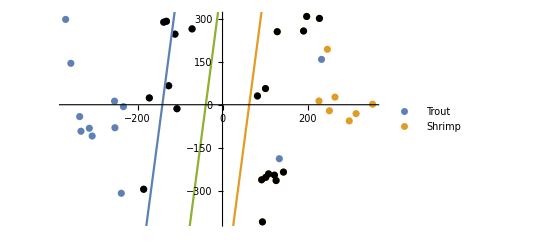

```mathematica
Show[ListPlot[Values[proj2FishChoiceBW],  PlotLegends ->Keys[proj2FishChoiceBW]],ListPlot[supportVectors2DBW3, PlotStyle -> Black],Plot[{Values[plusMargin2DBW3],Values[minusMargin2DBW3], Values[decisionLine2DBW3]},{x,Min[Values[data2DBW]], Max[Values[data2DBW]]}]]
```

#### Projecting test data

Now project the test data onto the graph

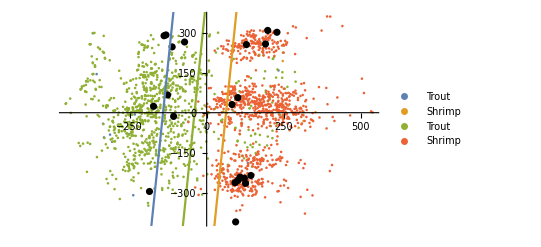

```mathematica
Show[ListPlot[Join[Values[proj2FishChoiceBW],Values[proj2TestChoiceBW]], PlotLegends ->Join[Keys[proj2FishChoiceBW], Keys[proj2TestChoiceBW]]],ListPlot[supportVectors2DBW3, PlotStyle -> Black],Plot[{Values[plusMargin2DBW3],Values[minusMargin2DBW3], Values[decisionLine2DBW3]},{x,Min[Values[data2DBW]], Max[Values[data2DBW]]}]]
```

#### Decision function

```mathematica
whichFish2DBW3[x_]:=Which[decision2DBW3[x][[1]] >0, fishChoice[[1]], True,fishChoice[[2]]]
```

```mathematica
Tally[Flatten[whichFish2DBW3 /@ proj2TestChoiceBW[[#]]& /@{1,2}]]
```

{{Shrimp,1114},{Trout,846}}

```mathematica
Tally[Join[Map[whichFish2DBW3[#] == Keys[proj2TestChoiceBW][[1]]&,proj2TestChoiceBW[[1]]], Map[whichFish2DBW3[#] == Keys[proj2TestChoiceBW][[2]]&,proj2TestChoiceBW[[2]]]]]
```

{{False,136},{True,1824}}

### Comparing

```mathematica
Tally[Join[Map[whichFish2DBW1[#] == Keys[proj2TestChoiceBW][[1]]&,proj2TestChoiceBW[[1]]], Map[whichFish2DBW1[#] == Keys[proj2TestChoiceBW][[2]]&,proj2TestChoiceBW[[2]]]]]
```

{{True,1866},{False,94}}

```mathematica
Tally[Join[Map[whichFish2DBW2[#] == Keys[proj2TestChoiceBW][[1]]&,proj2TestChoiceBW[[1]]], Map[whichFish2DBW2[#] == Keys[proj2TestChoiceBW][[2]]&,proj2TestChoiceBW[[2]]]]]
```

{{True,1847},{False,113}}

```mathematica
Tally[Join[Map[whichFish2DBW3[#] == Keys[proj2TestChoiceBW][[1]]&,proj2TestChoiceBW[[1]]], Map[whichFish2DBW3[#] == Keys[proj2TestChoiceBW][[2]]&,proj2TestChoiceBW[[2]]]]]
```

{{False,136},{True,1824}}

## Conclusion

The classify function is extremely accurate at determining the type of fish in this dataset. For the two classes that were focused on, we can conclude that the images are indeed suitable to work with in grayscale instead of colour. There was also no benefit to working with the 3D-reduced data. We explored the regularization parameter C for the support vector machines dual problem. We gathered that the higher this value is, the more support vectors are chosen in the model. When C increases the training error decreases but the test error increases. The optimal choice for this regularization parameter is not straight forward and further analysis on this topic would be worthwhile.

1-2

1	https://www.kaggle.com/crowww/a-large-scale-fish-dataset

2	A Large-Scale Dataset for Fish Segmentation and Classification,
Ulucan, Oguzhan and Karakaya, Diclehan and Turkan, Mehmet,
2020 Innovations in Intelligent Systems and Applications Conference (ASYU),
1--5,
2020,
IEEE